```mathematica
ListDevices[jfile_List]:=Module[{log},
log="log"/.jfile;
Select[DeleteDuplicates[("device"/.#)&/@log],#≠"device"&]
];
GetDeviceLog[deviceName_String,jfile_List]:=Module[{log},
log="log"/.jfile;
Select[log,("device"/.#)==deviceName&]
];
getVar[s_String,deviceLog_List,timeFit_FittedModel]:=
Module[{dList,vList},
dList=("data"/.#)& /@ deviceLog;
vList = Select[(s/.#)& /@ dList,Head[#]==List&];
{timeFit @("vartime"/.#), ("value"/.#)}& /@ vList
];
getAllVars[deviceLog_List,timeFit_FittedModel]:=
Module[{varList,dlist},
dlist=("data"/.#)& /@ deviceLog;
varList=Union[Table[i[[1]],{i,Select[Flatten[dlist],Head[#[[2]]]==List&]}]];
{varList,Table[DeleteDuplicates[getVar[v,deviceLog,timeFit]],{v,varList}]}
];
GetDeviceData[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13];
getAllVars[dev,timeFit]
];
GetTimeFit[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13]
];
```

```mathematica
PlotTimes[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
ListPlot[Transpose[{devServerTimes,deviceTimes}]]
];
```

```mathematica
GetDevTimes[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
"devicetime"/.("data"/.#)&/@dev
];
```

```mathematica
hvTimes=GetDevTimes["HV-LOWSIDE",jfile1];
```

```mathematica
FindBreaks[x_]:=Module[{b,n,i},
b={};
n=Length[x];
For[i=1, i<n,i++,
If[x[[i]]>x[[i+1]],AppendTo[b,i]]
];
b
]
```

```mathematica
GetDeviceDataRange[deviceName_String,jfile_List,toTake_]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{Take[deviceTimes,toTake],Take[devServerTimes,toTake]}],x,x,WorkingPrecision->13];
getAllVars[Take[dev,toTake],timeFit]
];
```

```mathematica
FindBreaks[GetDevTimes["HV-LOWSIDE",jfile1]]
```

{1965}

```mathematica
hv1a=GetDeviceDataRange["HV-LOWSIDE",jfile1,1965];
```

```mathematica
hv1a[[1]]
```

{cw_avg,cwc_avg,n,nst_rms,variac_rms}

```mathematica
hv1b=GetDeviceDataRange["HV-LOWSIDE",jfile1,-1123];
```

```mathematica
hv1b[[2,1;;5,1]]
```

{{295186.2357947,-1.37718},{295186.2357947,0.},{295186.2357947,61},{295185.2360259,0.0561853},{295185.2360259,0.792467}}

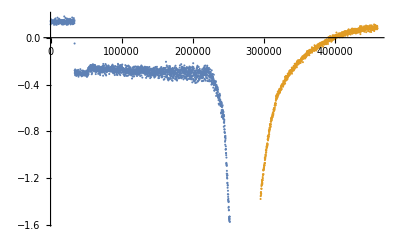

```mathematica
ListPlot[{hv1a[[2,1]],hv1b[[2,1]]},PlotRange->{All,All}]
```

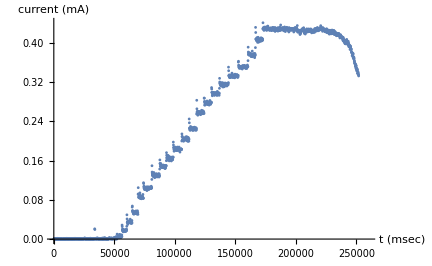

```mathematica
ListPlot[hv1a[[2,2]],PlotRange->{{0,260000},All},
AxesLabel->{"t (msec)","current (mA)"}]
```

```mathematica
cmd1=GetDeviceData["Command",jfile1];
```

```mathematica
cmd1[[2,3]]
```

{{20030.,#promote: tespelien},{25130.,TMP low},{33637.,variac:set:5.0},{33743.,variac:set:5.0},{45684.,variac:set:6.0},{52075.,variac:set:7.0},{56235.,variac:set:8.0},{60195.,variac:set:9.0},{64625.,variac:set:10.0},{69511.,variac:set:11.0},{73969.,variac:set:12.0},{80901.,variac:set:13.0},{87390.,variac:set:14.0},{92898.,variac:set:15.0},{98551.,variac:set:16.0},{105640.,variac:set:17.0},{111690.,variac:set:18.0},{117880.,variac:set:19.0},{124050.,variac:set:20.0},{130210.,variac:set:21.0},{136760.,variac:set:22.0},{144170.,variac:set:23.0},{152310.,variac:set:24.0},{160400.,variac:set:25.0},{166520.,variac:set:26.0},{172600.,variac:set:27.0},{181070.,TMP low},{200890.,TMP on},{287750.,variac:set:0.0}}

```mathematica
hv1a[[2,1;;5,-1]]
```

{{251974.162209,-1.5728},{251974.162209,0.332199},{251974.162209,60},{251974.162209,1.4788},{251974.162209,25.9156}}

```mathematica
FindBreaks[GetDevTimes["PIRANI",jfile1]]
```

{1779}

```mathematica
pirani1a = GetDeviceDataRange["PIRANI",jfile1,1779];
```

```mathematica
pirani1a[[1]]
```

{p2,p3,p4}

```mathematica
pirani1a[[2,1;;3,-1]]
```

{{257198.805419,-760.},{257263.871399,0.0223},{257339.948545,0.0223}}

```mathematica
ListDevices[jfile1]
```

{<reset>,PIRANI,HV-LOWSIDE,GAS,TMP,SENSORARRAY,HV-RELAY,RP,VARIAC,Heartbeat,Command,<promote>,Comment}

```mathematica
FindBreaks[GetDevTimes["GAS",jfile1]]
```

{251}

```mathematica
gas1a = GetDeviceDataRange["GAS",jfile1,251];
```

```mathematica
gas1a[[1]]
```

{nv_angle,nv_in,nv_ms,sol_in,sol_stat}

```mathematica
gas1a[[2,1,-1]]
```

{-443926.296146,0.}

```mathematica
FindBreaks[GetDevTimes["TMP",jfile1]]
```

{2184}

```mathematica
tmp1a = GetDeviceDataRange["TMP",jfile1,2184];
```

```mathematica
tmp1a[[1]]
```

{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp}

```mathematica
tmp1a[[2,1;;6,-1]]
```

{{257378.111965,False},{181106.809497,True},{257378.111965,1.43066},{257378.111965,128.174},{-174505.789641,False},{200923.196432,True}}

```mathematica
FindBreaks[GetDevTimes["HV-RELAY",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["RP",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["VARIAC",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["SENSORARRAY",jfile1]]
```

{}

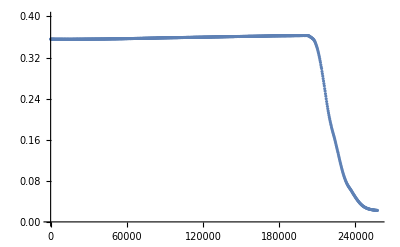

```mathematica
ListPlot[pirani1a[[2,3]],PlotRange->{All,{0,.4}}]
```

```mathematica
Take[pirani1a[[2,3]],-1]
```

{{257339.948545,0.0223}}

```mathematica
Take[hv1a[[2,1]],-1]
```

{{251974.162209,-1.5728}}

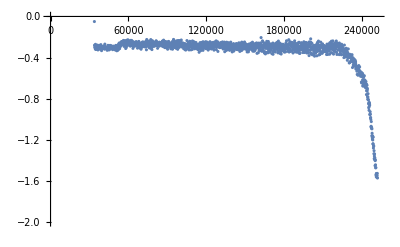

```mathematica
ListPlot[hv1a[[2,1]],PlotRange->{All,{-2,0}}]
```

```mathematica
hv1a[[2,1]]
```

{{59.0942366,0.112804},{183.064743,0.139055},{333.029066,0.145963},{456.9995727,0.125239},{583.9693658,0.128002},1955,{251597.251878,-1.54655},{251722.222147,-1.56796},{251847.192416,-1.5279},{251974.162209,-1.5728}}
 |  |  |  |

```mathematica
FindBreaks[hvTimes]
```

{1965}

```mathematica
Dimensions[hvTimes]
```

{3088}

```mathematica
jfile1 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-06-03T16-25-12_repeat of 8kv plasma test.json"];
```

```mathematica
jfile2 =Import["C:\\git\\EpsIo\\Fusor\\logs\\fusor-2021-06-06T16-43-42_last take (1).json"];
```

```mathematica
hvTimes2=GetDevTimes["HV-LOWSIDE",jfile2];
```

```mathematica
hv2=GetDeviceData["HV-LOWSIDE",jfile2];
```

```mathematica
hv2[[1]]
```

{cw_avg,cwc_avg,n,nst_rms,variac_rms}

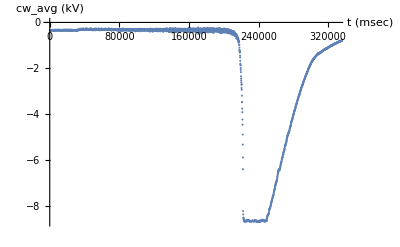

```mathematica
t2=240000;ListPlot[hv2[[2,1]],
PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,1]]" (kV)"}]
```

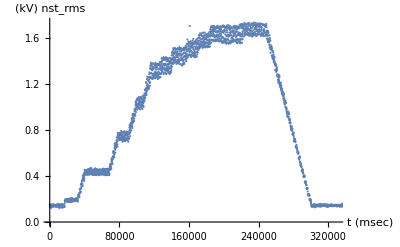

```mathematica
ListPlot[hv2[[2,4]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,4]]" (kV)"}]
```

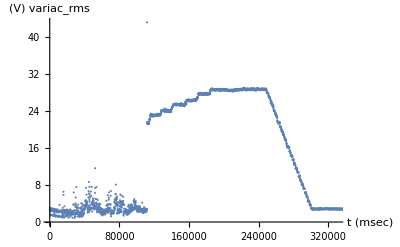

```mathematica
ListPlot[hv2[[2,5]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,5]]" (V)"}]
```

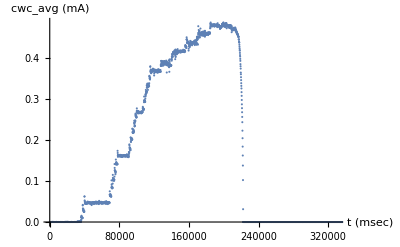

```mathematica
ListPlot[hv2[[2,2]],
PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,2]]" (mA)"}]
```

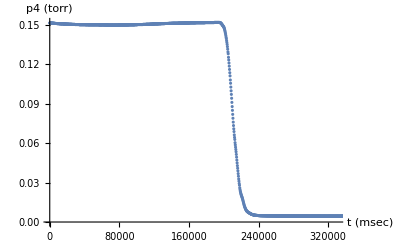

```mathematica
ListPlot[pirani2[[2,3]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",pirani2[[1,3]]" (torr)"}]
```

```mathematica
Take[pirani2[[2,3]],-2]
```

{{237795.158651,0.02218},{238081.445423,0.02215}}

```mathematica
pirani2=GetDeviceData["PIRANI",jfile2];
```

```mathematica
piraniTimes2=GetDevTimes["PIRANI",jfile2];
```

```mathematica
FindBreaks[piraniTimes2]
```

{}

```mathematica
cmd2=GetDeviceData["Command",jfile2]; cmd2[[1]]
```

{ip,observer,text}

```mathematica
tmp2=GetDeviceData["TMP",jfile2];
```

```mathematica
tmp2[[1]]
```

{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp}

```mathematica
tmp2[[2,1,-1]]
```

{388380.669154,False}

```mathematica
MatrixForm[cmd2[[2,3]]]
```

(10000. | variac:set:5.0
31160. | variac:set:10.0
68702. | variac:set:15.0
90262. | variac:set:20.0
106680. | variac:set:25.0
127390. | variac:set:26.0
139670. | variac:set:27.0
155510. | variac:set:28.0
168880. | variac:set:29.0
183150. | variac:set:30.0
194230. | TMP on
242590. | variac:set:1.0
381563. | TMP off
387716. | variac:set:0.0)

```mathematica
cmd1=GetDeviceData["Command",jfile1];cmd1[[1]]
```

{ip,observer,text}

```mathematica
ListDevices[jfile1]
```

{<reset>,Comment,VARIAC,GAS,Heartbeat,TMP,HV-RELAY,PIRANI,RP,SENSORARRAY,HV-LOWSIDE,Login,Command,<promote>}

```mathematica
sensor2=GetDeviceData["SENSORARRAY",jfile2];
```

```mathematica
sensor2[[1]]
```

{gc1,gc2,gc3,pin,pnj}

```mathematica
tx=220000;
```

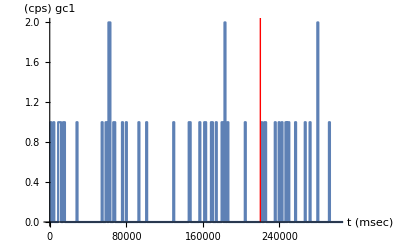

```mathematica
ListStepPlot[sensor2[[2,1]],PlotRange->{{0,300000},All},
Epilog->{Red,Line[{{tx,0},{tx,6}}]},
AxesLabel->{"t (msec)",sensor2[[1,1]]" (cps)"}]
```

```mathematica
pressure2=Interpolation[pirani2[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
hvVsP2=Table[{pressure2[x[[1]]],-x[[2]]},{x,Drop[hv2[[2,1]],-1000]}];
```

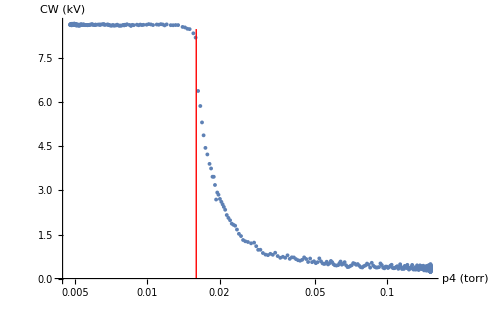

```mathematica
px=0.016;ListPlot[hvVsP2,PlotRange->{All,All},
ScalingFunctions->{"Log",None},
Epilog->{Red,Line[{{Log[px],0},{Log[px],8.5}}],
Text[1000 px "microns",{Log[px],9}]},
AxesLabel->{"p4 (torr)","CW (kV)"}]
```

```mathematica
current2=Interpolation[hv2[[2,2]]]
```

InterpolatingFunction[…]

```mathematica
hvVsCurrent2=Table[{current2[x[[1]]],-x[[2]]},{x,hv2[[2,1]]}];
```

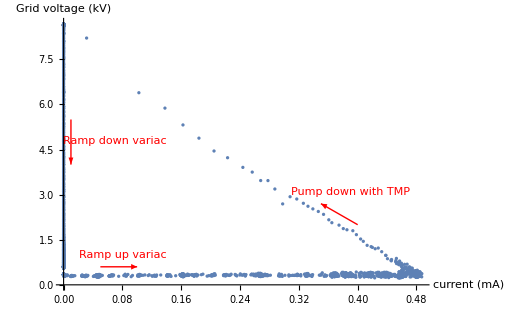

```mathematica
ListPlot[hvVsCurrent2,PlotRange->All,PlotStyle->Large,
AxesLabel->{"current (mA)","Grid voltage (kV)"},
Epilog->{Red,Thick,
Arrow[{{0.05,0.6},{0.1,0.6}}],Text["Ramp up variac",{0.08,1.0}],
Arrow[{{0.4,2},{0.35,2.7}}],Text["Pump down with TMP",{0.39,3.1}],
Arrow[{{0.01,5.5},{0.01,4}}],Text["Ramp down variac",{0.07,4.8}]
}]
```